```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metaStructure2={Number,Number,Number,Number,Number,Number,Number,Word,Real};
metaStructure3={Real,Real,Real,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desc3.dat"],metaStructure2];
metalvl3={Real,Real,Real,Real,Real,Real,Real,Real};
ts={35,50,65,80,95,110,125,140,155,170,180,200,215,220,230,240,245,260,275,280,290,300,305,320,335,340,350,360,365,380};
tssz=Dimensions[ts][[1]];
tsadd=PlusMinus[11.3,0.397];
(*Print["Executing: ts = ",ts[[i]]," , i = ",i];*)
tfal=ReadList[StringJoin[descDir,seperator,"tf-Al.dat"],metaStructure3];
tfcu=ReadList[StringJoin[descDir,seperator,"tf-Cu.dat"],metaStructure3];
tk2[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~Table[{10^j,"",{c,d}},{j,l-N[Log10[2]],u+N[Log10[2]],int}]],3];
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

## Sample Signal

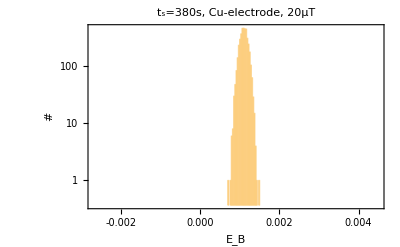

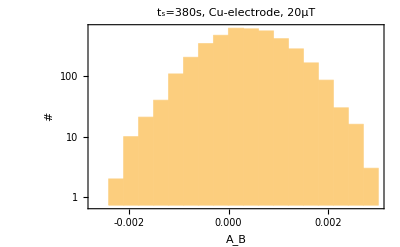

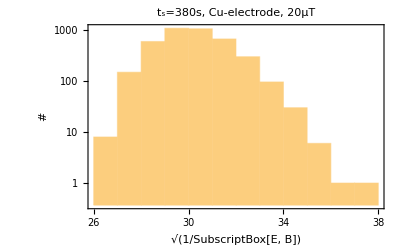

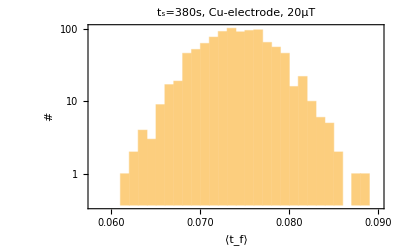

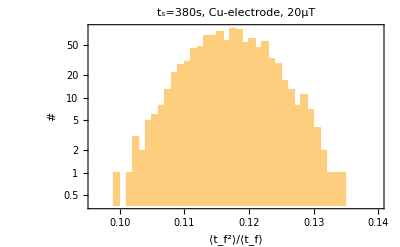

-6.70563×10^13+6.80078×10^11 x-2.8608×10^9 x^2+6.17313×10^6 x^3-6313.87 x^4+0.36461 x^5+0.00472737 x^6-1.18551×10^-6 x^7-3.66208×10^-9 x^8+4.79848×10^-13 x^9+2.97247×10^-15 x^10+4.42652×10^-19 x^11-2.22781×10^-21 x^12-1.06674×10^-24 x^13+1.5014×10^-27 x^14+1.2489×10^-30 x^15-1.1223×10^-33 x^16-1.04205×10^-36 x^17+1.50133×10^-39 x^18-6.40598×10^-43 x^19+9.7021×10^-47 x^20

335/2

325/2

325/2

```mathematica
i=16;
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
maxsz=1000;
maxsz3=4000;
(*maxsz2=100000;*)
tf=Table[0,{k,1,maxsz}];
tf2tf=Table[0,{k,1,maxsz}];
If[i≤15,
kk=Position[tfal,descdat[[i]][[7]]+2*tsadd[[1]]][[1]][[1]];
tf=RandomVariate[NormalDistribution[tfal[[kk]][[2]],tfal[[kk]][[4]]],maxsz];
tf2tf=RandomVariate[NormalDistribution[tfal[[kk]][[5]],tfal[[kk]][[7]]],maxsz];
,
kk=Position[tfcu,descdat[[i]][[7]]+2*tsadd[[1]]][[1]][[1]];
tf=RandomVariate[NormalDistribution[tfcu[[kk]][[2]],tfcu[[kk]][[4]]],maxsz];
tf2tf=RandomVariate[NormalDistribution[tfcu[[kk]][[5]],tfcu[[kk]][[7]]],maxsz];
];
(***)
ab=RandomVariate[NormalDistribution[lvl3[[1]][[1]],lvl3[[1]][[2]]],maxsz3];
eb=RandomVariate[NormalDistribution[lvl3[[1]][[3]],lvl3[[1]][[4]]/10],maxsz3];
(*eb=RandomVariate[NormalDistribution[.0004,.00001],maxsz3];*)
tftseb0=Flatten[KroneckerProduct[1/eb,(descdat[[i]][[7]]+2tsadd[[1]])*tf2tf]];
tftsab=Flatten[KroneckerProduct[1/ab,(descdat[[i]][[7]]+2tsadd[[1]])/tf]];
tftseb=Flatten[KroneckerProduct[1/eb,(descdat[[i]][[7]]+2tsadd[[1]])/tf]];
Histogram[eb,{-.0027,.0045,.00003},PlotRange->Full,PlotRange->Full,Frame->True,FrameLabel->{"E_B","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[ab,{-.0027,.003,.0003},PlotRange->Full,PlotRange->Full,Frame->True,FrameLabel->{"A_B","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[Sqrt[1/eb],PlotRange->Full,Frame->True,FrameLabel->{"√(1/SubscriptBox[E, B])","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[tf,{.058,.09,.001},PlotRange->{{.058,.09},Automatic},Frame->True,FrameLabel->{"⟨t_f⟩","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[tf2tf,{.096,.14,.001},PlotRange->{Automatic,Automatic},Frame->True,FrameLabel->{"⟨t_f^2⟩/⟨t_f⟩","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
(*Histogram[Sqrt[tftseb0]]
Histogram[Sqrt[tftsab]]
Histogram[Sqrt[tftseb]]*)


(*****************************************)
sigma=10;rr=10;
histlst=HistogramList[Sqrt[tftseb0]];
hstbl=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+4.2 histlst[[1]][[k]],histlst[[2]][[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
fthst=Fit[hstbl,Table[x^k,{k,0,20,1}],x]
fthst2=Interpolation[hstbl,InterpolationOrder->2];
estbckp=EstimatedBackground[hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm=-EstimatedBackground[-hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm2=-EstimatedBackground[-estbckm,10,Method->{"SNIP",10}];
ptbckp=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckp[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm2=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm2[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
histhisttftseb0tot=Total[estbckm2];
cumhisttftseb0t=ParallelTable[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],Total[estbckm2[[;;k]]]/histhisttftseb0tot},{k,1,Dimensions[histlst][[1]]}];
val90=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val90]][[1]]]][[1]]
val95=Nearest[cumhisttftseb0t[[;;,2]],0.05][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val95]][[1]]]][[1]]
val99=Nearest[cumhisttftseb0t[[;;,2]],0.01][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val99]][[1]]]][[1]]
```

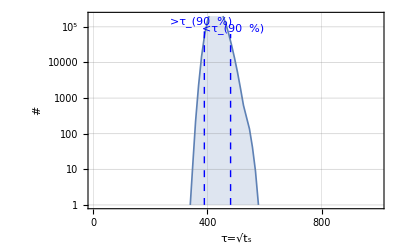

```mathematica
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{389,Log@(10^0)},{389,Log@(10^5.05)}}];
line2=Line[{{481,Log@(10^0)},{481,Log@(10^4.8)}}];
line3=Line[{{194,Log@(10^0)},{194,Log@(10^2.7)}}];
plotsamepic=ListLinePlot[{Join[Table[{10k,.1},{k,0,10}],(hstbl)/2]},Frame->True,FrameLabel->{"τ=√t_s","#"},PlotRange->{{1,999},{1,2*10^5}},PlotStyle->Thickness[.003],Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},
Epilog->{
{Directive[lineStyle1],line1,Style[Text[">τ_(90  %)",{379,Log@(10^5.15)}],Large]},
{Directive[lineStyle1],line2,Style[Text["<τ_(90  %)",{491,Log@(10^4.95)}],Large]}
}]
```

# σ(<t_f>) -> x2

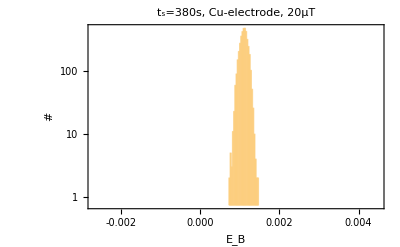

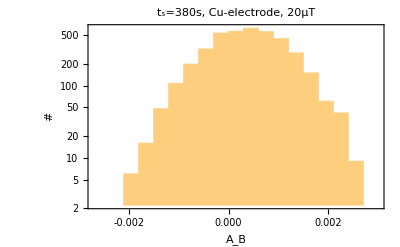

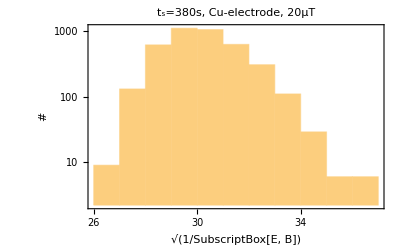

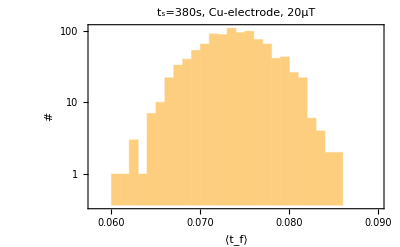

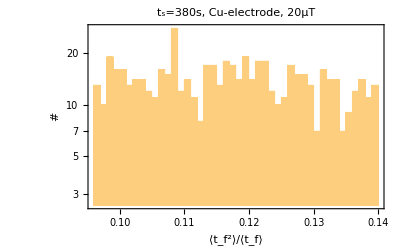

-6.89538×10^10+1.33371×10^9 x-1.16164×10^7 x^2+59974.2 x^3-202.822 x^4+0.466379 x^5-0.00072476 x^6+7.07852×10^-7 x^7-3.0928×10^-10 x^8-1.51415×10^-13 x^9+2.5021×10^-16 x^10-2.34261×10^-20 x^11-1.28366×10^-22 x^12+4.78545×10^-26 x^13+5.92228×10^-29 x^14-4.37308×10^-32 x^15-1.86176×10^-35 x^16+3.64004×10^-38 x^17-1.95866×10^-41 x^18+4.97411×10^-45 x^19-5.11051×10^-49 x^20

105

95

95

```mathematica
i=16;
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
maxsz=1000;
maxsz3=4000;
(*maxsz2=100000;*)
tf=Table[0,{k,1,maxsz}];
tf2tf=Table[0,{k,1,maxsz}];
If[i≤15,
kk=Position[tfal,descdat[[i]][[7]]+2*tsadd[[1]]][[1]][[1]];
tf=RandomVariate[NormalDistribution[tfal[[kk]][[2]],tfal[[kk]][[4]]],maxsz];
tf2tf=RandomVariate[NormalDistribution[tfal[[kk]][[5]],tfal[[kk]][[7]]],maxsz];
,
kk=Position[tfcu,descdat[[i]][[7]]+2*tsadd[[1]]][[1]][[1]];
tf=RandomVariate[NormalDistribution[tfcu[[kk]][[2]],tfcu[[kk]][[4]]],maxsz];
tf2tf=RandomVariate[NormalDistribution[tfcu[[kk]][[5]],tfcu[[kk]][[7]]],maxsz];
];
(***)
ab=RandomVariate[NormalDistribution[lvl3[[1]][[1]],lvl3[[1]][[2]]],maxsz3];
eb=RandomVariate[NormalDistribution[lvl3[[1]][[3]],lvl3[[1]][[4]]/5],maxsz3];
(*eb=RandomVariate[NormalDistribution[.0004,.00001],maxsz3];*)
tftseb0=Flatten[KroneckerProduct[1/eb,(descdat[[i]][[7]]+2tsadd[[1]])*tf2tf]];
tftsab=Flatten[KroneckerProduct[1/ab,(descdat[[i]][[7]]+2tsadd[[1]])/tf]];
tftseb=Flatten[KroneckerProduct[1/eb,(descdat[[i]][[7]]+2tsadd[[1]])/tf]];
Histogram[eb,{-.0027,.0045,.00003},PlotRange->Full,PlotRange->Full,Frame->True,FrameLabel->{"E_B","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[ab,{-.0027,.003,.0003},PlotRange->Full,PlotRange->Full,Frame->True,FrameLabel->{"A_B","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[Sqrt[1/eb],PlotRange->Full,Frame->True,FrameLabel->{"√(1/SubscriptBox[E, B])","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[tf,{.058,.09,.001},PlotRange->{{.058,.09},Automatic},Frame->True,FrameLabel->{"⟨t_f⟩","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[tf2tf,{.096,.14,.001},PlotRange->{Automatic,Automatic},Frame->True,FrameLabel->{"⟨t_f^2⟩/⟨t_f⟩","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
(*Histogram[Sqrt[tftseb0]]
Histogram[Sqrt[tftsab]]
Histogram[Sqrt[tftseb]]*)


(*****************************************)
sigma=10;rr=10;
histlst=HistogramList[Sqrt[tftseb0]];
hstbl=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+4.2 histlst[[1]][[k]],histlst[[2]][[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
fthst=Fit[hstbl,Table[x^k,{k,0,20,1}],x]
fthst2=Interpolation[hstbl,InterpolationOrder->2];
estbckp=EstimatedBackground[hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm=-EstimatedBackground[-hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm2=-EstimatedBackground[-estbckm,10,Method->{"SNIP",10}];
ptbckp=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckp[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm2=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm2[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
histhisttftseb0tot=Total[estbckm2];
cumhisttftseb0t=ParallelTable[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],Total[estbckm2[[;;k]]]/histhisttftseb0tot},{k,1,Dimensions[histlst][[1]]}];
val90=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val90]][[1]]]][[1]]
val95=Nearest[cumhisttftseb0t[[;;,2]],0.05][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val95]][[1]]]][[1]]
val99=Nearest[cumhisttftseb0t[[;;,2]],0.01][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val99]][[1]]]][[1]]
```

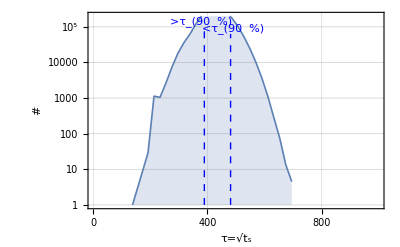

```mathematica
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{389,Log@(10^0)},{389,Log@(10^5.05)}}];
line2=Line[{{481,Log@(10^0)},{481,Log@(10^4.8)}}];
line3=Line[{{194,Log@(10^0)},{194,Log@(10^2.7)}}];
plotsamepic2=ListLinePlot[{Join[Table[{10k,.1},{k,0,10}],(hstbl)/2]},Frame->True,FrameLabel->{"τ=√t_s","#"},PlotRange->{{1,999},{1,2*10^5}},PlotStyle->Thickness[.003],Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},
Epilog->{
{Directive[lineStyle1],line1,Style[Text[">τ_(90  %)",{379,Log@(10^5.15)}],Large]},
{Directive[lineStyle1],line2,Style[Text["<τ_(90  %)",{491,Log@(10^4.95)}],Large]}
}]
```

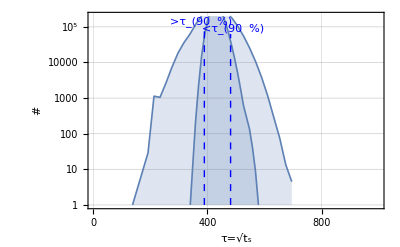

```mathematica
Show[plotsamepic,plotsamepic2]
```